```mathematica
data=Import["/home/phyks/hackEns/CitizenWatt/sample_emontxv2/samples/sample_power_only.log", "List"]
```

{478,477,477,477,477,476,476,478,476,478,476,477,478,477,476,477,476,477,475,476,452,452,451,452,450,450,449,449,449,449,450,450,450,447,450,451,449,450,450,448,448,449,448,449,451,449,447,448,448,448,447,458,448,448,472,445,447,445,447,446,444,446,445,444,446,447,447,445,444,444,444,445,445,445,«37927»,133,134,136,134,136,136,137,137,132,136,134,134,134,137,105,103,105,105,104,104,103,104,105,103,103,104,104,138,140,140,140,138,142,141,138,139,142,140,138,138,139,140,142,140,139,140,140,141,139,139,141,141,141,140,139,139,137,140,140,139,139,140,137,138,176,176,176,176,173,176,175,175,177,175}

```mathematica
dataIntegrate=Table[{n,data[[n]]},{n,1,Length[data]}]
```

{{1,478},{2,477},{3,477},{4,477},{5,477},{6,476},{7,476},{8,478},{9,476},{10,478},{11,476},{12,477},{13,478},{14,477},{15,476},{16,477},{17,476},{18,477},{19,475},{20,476},{21,452},{22,452},{23,451},{24,452},{25,450},{26,450},{27,449},{28,449},«38019»,{38048,140},{38049,141},{38050,139},{38051,139},{38052,141},{38053,141},{38054,141},{38055,140},{38056,139},{38057,139},{38058,137},{38059,140},{38060,140},{38061,139},{38062,139},{38063,140},{38064,137},{38065,138},{38066,176},{38067,176},{38068,176},{38069,176},{38070,173},{38071,176},{38072,175},{38073,175},{38074,177},{38075,175}}

```mathematica
N[Integrate[Interpolation[dataIntegrate,InterpolationOrder->20][x],{x,1,Length[data]}]]/1000/3600
```

1.63985

```mathematica
N[Integrate[Interpolation[dataIntegrate,InterpolationOrder->2][x],{x,1,Length[data]}]]/1000/3600
```

1.63459

```mathematica
(1.6398545285039345-1.634589976851852)/1.634589976851852*100
```

0.322072

```mathematica
interpol=Interpolation[dataIntegrate,InterpolationOrder->20]
```

InterpolatingFunction[{{1,38075}},<>]

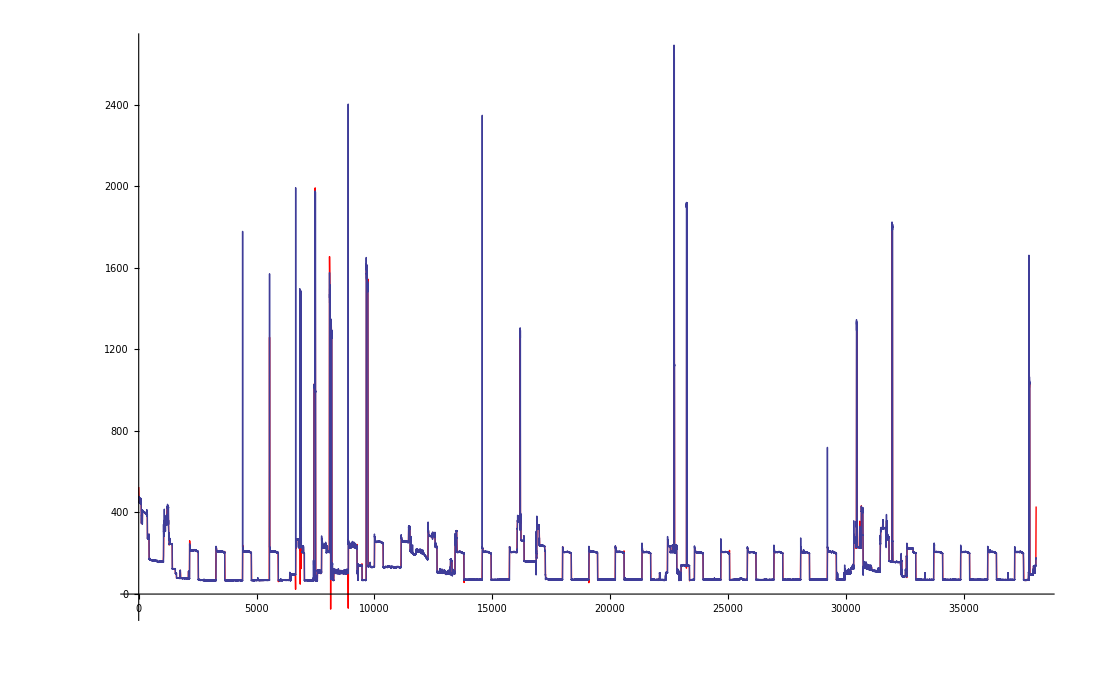

```mathematica
Show[Plot[interpol[x],{x,1,Length[data]},PlotStyle->Red,PlotRange->All],ListLinePlot[data, PlotRange->All],PlotRange->All]
```

```mathematica
Length[data]
```

38075

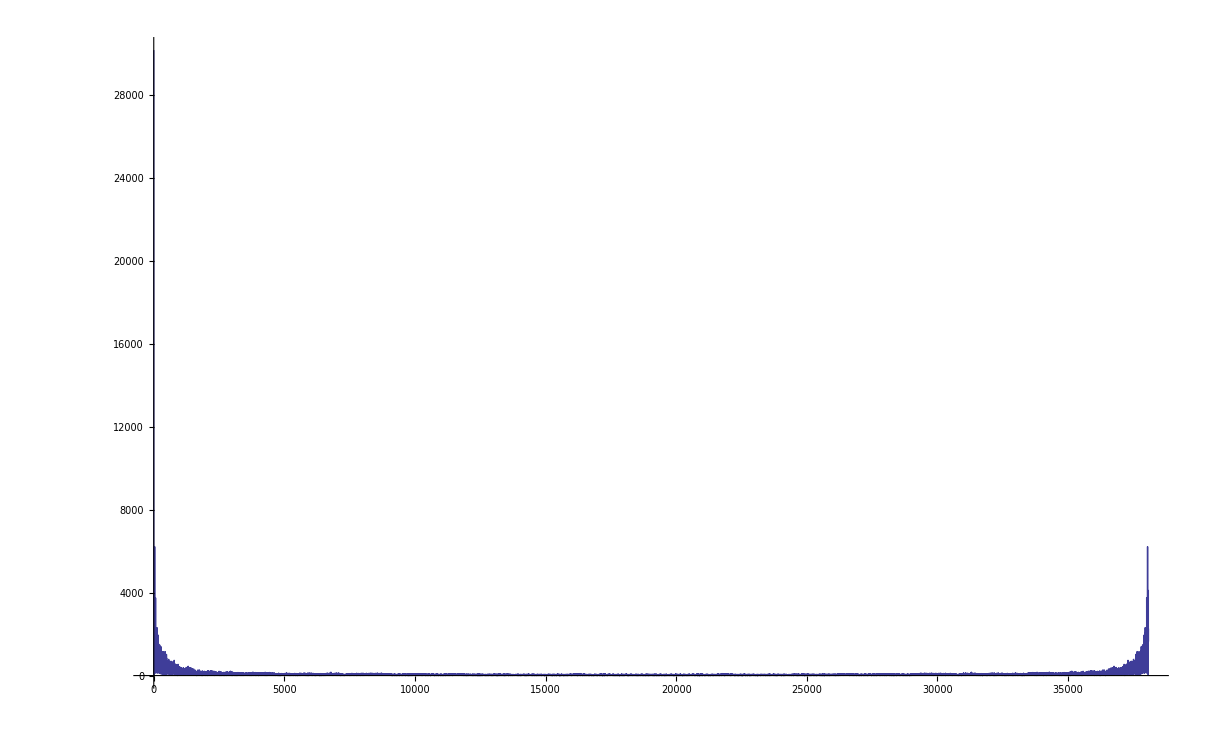

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->All]
```

```mathematica
ListLinePlot[data,PlotRange->All]
```

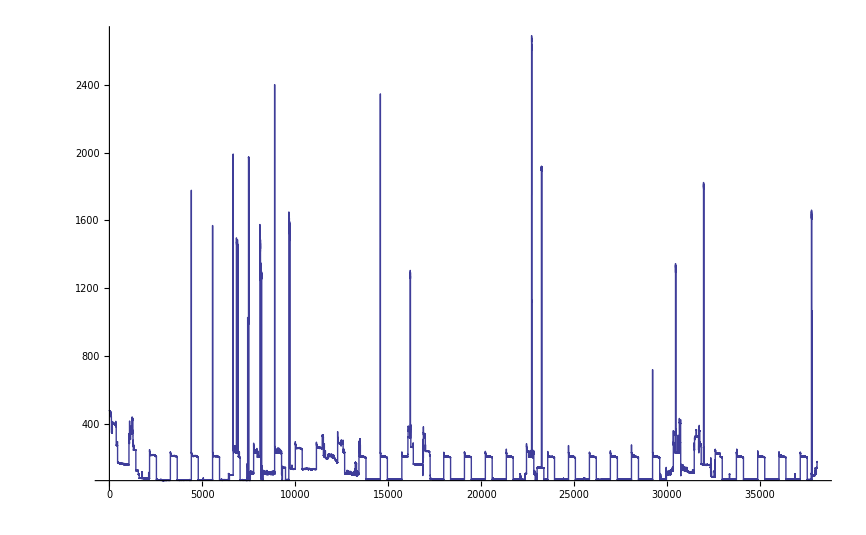
```mathematica
-Graphics-f
```

```mathematica
fftshift1D[array_]:=Module[{len=Length[array]},If[EvenQ[len],RotateRight[array,len/2],RotateRight[array,(len-1)/2]]]
```

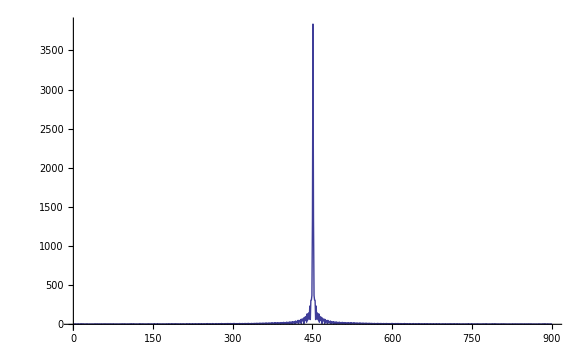

```mathematica
ListLinePlot[fftshift1D[Abs[Fourier[data[[2150;;3050]]]]], PlotRange->Full]
```

```mathematica
Max[Abs[Fourier[data[[1550;;3050]]]]]
```

4237.05

```mathematica
1/(2*%)
```

0.000118007